-Graphics-
-Graphics-
-Graphics-

Задим начальные значения

```mathematica
Variant = 3.29;
n = 6;
c[i_,j_]:= 0.1*Variant*i*j;
a[i_,j_]= 10/(0.3*c[i,j]^3+10c[i,j]);
A=Table[a[i,j],{i,1,n},{j,1,n}];
b=Table[Variant,{i,1,n}];
```

Сотавим программу для решения СЛАУ методом Гаусса (Предпологаем, что нулевых элементов нет)

```mathematica
GaussMethod[M_,m_]:=(
If[Or[Length[M] ≠ Length[m],SquareMatrixQ[M]==False],Return["Cannot solve"]];
a = Transpose[Append[A,{m[[1]],m[[2]],m[[3]],m[[4]],m[[5]],m[[6]]}]]; 
(*a = Transpose@Append[Transpose@A,{b[[1]],b[[2]],b[[3]],b[[4]],b[[5]],b[[6]]}];*)
n = Length[M];2
For[k=1,k≤n,k++,h=k;max=Abs[a[[k,k]]];
For[i=k+1,i≤n,i++,If[Abs[a[[i,k]]]>max,{h=i,max=Abs[a[[i,k]]]}]];
If[h≠k,For[j=k,j≤n+1,j++,{w=a[[k,j]],a[[k,j]]=a[[h,j]],a[[h,j]]=w}]];
For[j=n+1,j≥k,j--,a[[k,j]]=a[[k,j]]/a[[k,k]]];
For[i=1,i≤n,i++,If[i≠k,For[j=n+1,j≥k,j--,a[[i,j]]=a[[i,j]]-a[[i,k]]*a[[k,j]]]]];];

Return[Transpose[a][[-1]]];
);
```

Найдем решения используя встроенные функции пакета

```mathematica
ExactX = LinearSolve[A,b];
MatrixForm@ExactX
```

(48.7054
-230.409
526.685
-845.633
773.69
-311.395)

Найдем число обусловленности матрицы

```mathematica
cond = LinearAlgebra`MatrixConditionNumber[A]
```

1.6646×10^6

```mathematica
X = GaussMethod[A,b];
MatrixForm@X
```

(48.7054
-230.409
526.685
-845.633
773.69
-311.395)

Выполним пункт 3

```mathematica
Δ=10^-5;
d[i_]:=(
NullVector = {0,0,0,0,0,0};
NullVector[[i]]=Δ;
Newb = NullVector+b;
x = GaussMethod[A,Newb];
MatrixForm@x;
Return[Max[ExactX-x]/Max[ExactX]];
;)
```

{0.0000202994,0.00017908,0.000541694,0.00101577,0.000699237,0.000290099}

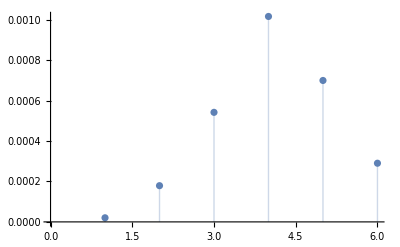

```mathematica
HistogramD = {d[1],d[2],d[3],d[4],d[5],d[6]}

Histogram[HistogramD];  (*Ничего особо не понятно, поэтому лучше использовать ListPlot*)
ListPlot[HistogramD,Filling->Axis]
```

Оценим теоретическую погрешность

```mathematica
error = {cond*Δ,cond*Δ,cond*Δ,cond*Δ,cond*Δ,cond*Δ}; (*Как строить этот вектор?!*)
Print[MatrixForm@error,MatrixForm@HistogramD]
```

(16.646
16.646
16.646
16.646
16.646
16.646)(0.0000202994
0.00017908
0.000541694
0.00101577
0.000699237
0.000290099)